## ShowEdgeNormal-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51f (14 June 2017)) loaded Wed 14 Jun 2017 12:44:47
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

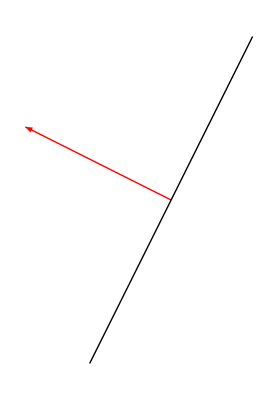

```mathematica
ShowEdgeNormal[{{1,1}, {2,3}}, {Red, Thick}, True]
```

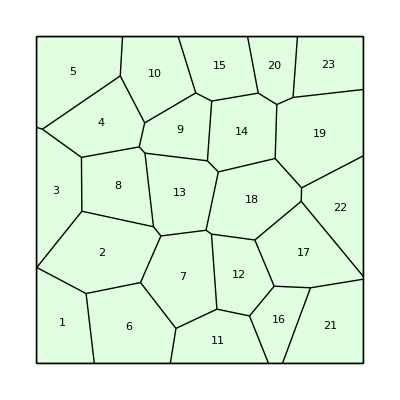

```mathematica
T=TemplateRandomSquareGrid[25, {0,0}, {10,10}];
ShowTissue[T, "CellNumbers"-> True]
```

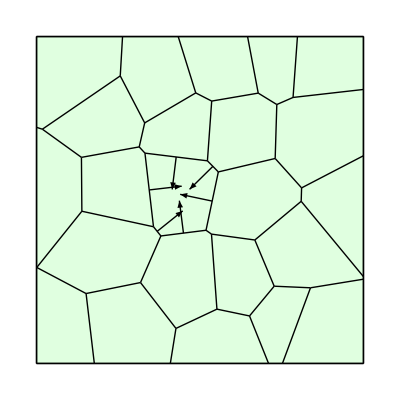

```mathematica
Show[
ShowTissue[T], 
ShowEdgeNormal/@Partition[CellVertexCoordinates[T,13], 2,1,1]
]
```

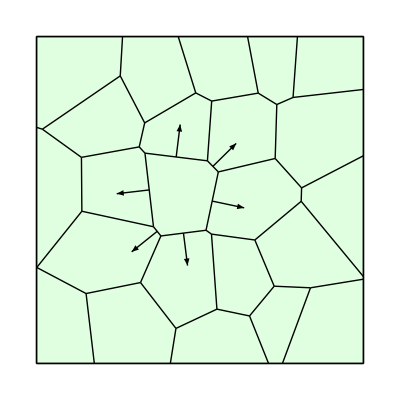

```mathematica
Show[
ShowTissue[T], 
ShowEdgeNormal/@Partition[Reverse[CellVertexCoordinates[T,13]], 2,1,1]
]
```